```mathematica
(*Approximation by Legendre Polynomial*)
```

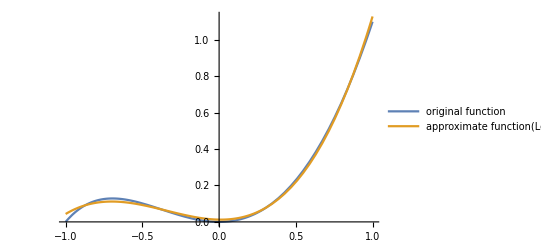

```mathematica
list1=LegendreP[#,x]&/@Range[0,3];
For[i=1,i≤4,i++,a[i]=NIntegrate[x^2 Log[2+x]*list1[[i]],{x,-1,1}]/NIntegrate[list1[[i]]^2,{x,-1,1}]]
g1=Sum[list1[[i]]*a[i],{i,1,4}]//Simplify;
Plot[{x^2*Log[x+2],g1},{x,-1,1},PlotLegends->Placed[{"original function","approximate function(Legendre)"},Center]]
```

```mathematica
(*Approximation by Tchebyshev Polynomial*)
```

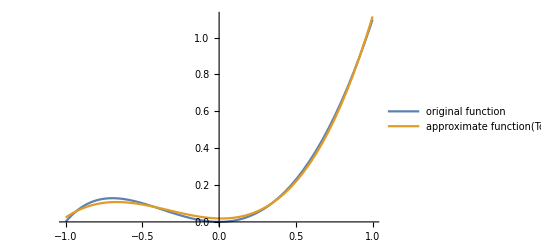

```mathematica
list2=ChebyshevT[#,x]&/@Range[0,3];
For[i=1,i≤4,i++,a[i]=NIntegrate[(x^2 Log[2+x]*list2[[i]])/(√(1-x^2)),{x,-1,1}]/NIntegrate[list2[[i]]^2/(√(1-x^2)),{x,-1,1}]]
g2=Sum[list2[[i]]*a[i],{i,1,4}]//Simplify;
Plot[{x^2*Log[x+2],g2},{x,-1,1},PlotLegends->Placed[{"original function","approximate function(Tchebyshev)"},Center]]
```

```mathematica
(*Approximation by Lagrange Interpolation *)
```

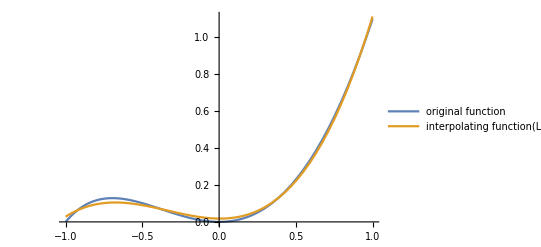

```mathematica
list3=Cos[#]&/@Table[((2 k -1)π)/8,{k,1,4}]//N;
list4=#^2*Log[#+2]&/@list3;
For[i=1,i≤4,i++,
For[{j=1,L[i,x]=1},j≤4,j++,If[j≠i,L[i,x]=L[i,x]*(x-list3[[j]])/(list3[[i]]-list3[[j]])]]]
Lagrange=Sum[list4[[i]]*L[i,x],{i,1,4}]//N//Expand;
Plot[{x^2*Log[x+2],Lagrange},{x,-1,1},PlotLegends->Placed[{"original function","interpolating function(Lagrange)"},Center]]
```

```mathematica
(*error comparison*)
```

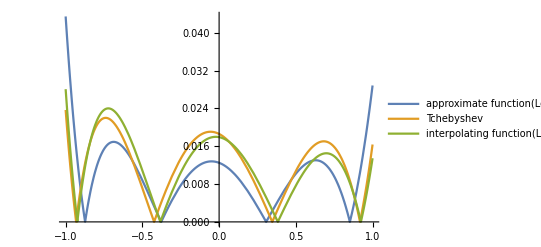

```mathematica
Plot[{Abs[g1-x^2*Log[x+2]],Abs[g2-x^2*Log[x+2]],Abs[Lagrange-x^2*Log[x+2]]},{x,-1,1},PlotLegends->Placed[{"approximate function(Legendre)","Tchebyshev","interpolating function(Lagrange)"},Center]]
```